## Steps for city generation

1. Start with a random base using a noise randomizer
	a. need to decide structure
	b. possible choices: tiling with each tile representing a different thing, polygons(nodes from that one article) 
2. From the base, generate more of the city
	a. Again we can use the nodes article where we can classify areas
	b. We can use wave function collapse: https://community.wolfram.com/groups/-/m/t/2435403
		wave function collapse is supposed to be easily compatible due to allowing support constraints so try my best to do that
* if we have extra time, add an option to be able to manually choose which base structure we start with.

possible tiles:
- street
- road
- building

### Perlin noise function(generating base city)

```mathematica
permutation = RandomSample[Range[1, 255]];
p = Join[permutation, permutation]; (*repeat it to avoid overflow*)
repeat = 255;
fade[t_] := t*t*t*(t*(t*6-15)+10); (* THE FADE FUNCTION >:) *)
inc[n_] := Module[{num = n+1}, If[repeat >0, num = Mod[num, repeat]]];
grad[hash_, x_, y_, z_] := Module[{hashy = BitAnd[hash,15 ]}, 
Which[
hashy==0, x+y,
hashy==1, -x+y,
hashy==2, x-y,
hashy==3, -x-y,
hashy==4, x+z,
hashy==5, -x+z,
hashy==6, x-z,
hashy==7, -x-z,
hashy==8, y+z,
hashy==9, -y+z,
hashy==10, y-z,
hashy==11,-y-z,
hashy==12,y+x,
hashy==13,-y+z,
hashy==14,y-x,
hashy==15,-y-z]];
lerp[a_,b_,x_] :=a+x*(b-a);
```

```mathematica
perlin[a_, b_, c_] := Module[{xi = Min[Floor[a], 254], yi = Min[Floor[b], 254], zi = Min[Floor[c], 254], aaa, aba, aab, abb, baa, bba, bab, bbb, x1, x2, y1, y2, x=a, y=b, z=c, xf, yf, zf, u, v, w},If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}];  
xf = x-Floor[x];yf = y-Floor[y];zf = z-Floor[z]; 
u = fade[xf]; v = fade[yf]; w = fade[zf];
aaa =p[[p[[p[[        xi   +1]]+yi+1]]+        zi    +1]]; aba = p[[p[[p[[xi+1]]+inc[yi]+1]]+zi+1]]; aab=p[[p[[p[[         xi   +1]]+yi+1]]+inc[zi]+1]]; abb=p[[p[[p[[xi+1]]+inc[yi]+1]]+inc[zi]+1]]; baa=p[[p[[p[[inc[xi]+1]]+yi+1]]+          zi  +1]]; bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+zi+1]]; bab=p[[p[[p[[inc[xi]+1]]+yi+1]]+inc[zi]+1]]; bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];
x1 = lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf], u];
x2 = lerp[grad[aba, xf, yf-1, zf], grad[bba, xf-1, yf-1, zf],u];
y1 = lerp[x1, x2, v];
x1 = lerp[grad[aab, xf, yf, zf-1], grad[bab, xf-1, yf, zf-1], u];
x2 = lerp[grad[abb, xf, yf-1, zf-1], grad[abb, xf, yf-1, zf-1], u];
y2 = lerp[x1, x2, v];
Rescale[lerp[y1, y2, w], {-1.2, 1.2}]];
```

```mathematica
octavePerlin[x_,y_,z_,octaves_,persistence_]:=Module[{total=0, frequency=1,amplitude=1,maxValue=0},
total = perlin[x*frequency,y*frequency,z*frequency]*amplitude + Total[Table[maxValue+= amplitude;amplitude*=persistence;frequency*=2;perlin[x*frequency,y*frequency,z*frequency]*amplitude, {i,octaves-1}]]; total/maxValue];
```

```mathematica
octaves=RandomInteger[{2, 3}];persistence=RandomReal[{0.2,0.4}];
ex = Table[octavePerlin[RandomInteger[{0, 10}], RandomInteger[{0, 10}], RandomReal[{0, 10}], octaves, persistence], 10];
Max[ex]
Min[ex]
Mean[ex]
```

```mathematica
perlin[1,2,0.010]
```

0.495837

```mathematica
Plot3D[octavePerlin[x,y,250,6,0.8],{x,20,21},{y,10,11}]
```

-Graphics3D-

```mathematica
Plot3D[octavePerlin[x,y,0.06,6,0.6],{x,22,21},{y,10,11}]
```

-Graphics3D-

### Road generation(binary recursion+perlin noise)

```mathematica
generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=Module[{stack,roads={},noise,smoothstep,jitter,clamp,pickAxis,addVerticalRoad,addHorizontalRoad,pushChildren,roadAdded=False, sizeFactor},
    
  noise[x_,z_]:=octavePerlin[x*noiseFreq,z*noiseFreq,0,4,0.5];
  
  smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
  
  jitter[max_]:=RandomReal[{-max,max}];
  
  clamp[val_,min_,max_]:=Min[Max[val,min],max];
  
  pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
  
  addVerticalRoad[x_,yStart_,yEnd_,width_]:=(AppendTo[roads,{Max[x, 1],Max[yStart, 1],Max[x, 1],yEnd,width}]; roadAdded=True);
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=(AppendTo[roads,{Max[xStart, 1],Max[y, 1],xEnd,Max[y, 1],width}]; roadAdded=True);
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];

  stack={{0,0,worldWidth,worldHeight}};

  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit},
    R=First[stack];
    stack=Rest[stack];
    
    n=noise[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2];
sizeFactor=Min[(R[[3]]/minBlock)+(R[[4]]/minBlock),2];
(*sizeFactor=Echo[smoothstep[1,2,Min[R[[3]]/minBlock,R[[4]]/minBlock]]];*)
(*sizeFactor=1;*)
    Psplit=smoothstep[lowCutoff,highCutoff,n]*sizeFactor;
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  (* Ensure at least one road is added *)
  If[!roadAdded,
   dir=pickAxis[{0,0,worldWidth,worldHeight}];
   If[dir=="vertical",
    xSplit=clamp[worldWidth/2+jitter[maxJitter],minBlock,worldWidth-minBlock];
    addVerticalRoad[xSplit,0,worldHeight,roadWidth],
    ySplit=clamp[worldHeight/2+jitter[maxJitter],minBlock,worldHeight-minBlock];
    addHorizontalRoad[0,ySplit,worldWidth,roadWidth]
    ];
   ];
  
  roads
  ]
```

## Map Generation(appl of funcs)

```mathematica
worldWidth=250;
worldHeight=250;
minBlock=10;
maxJitter=5;
roadWidth=2;
noiseFreq=0.1;
lowCutoff=0.2;
highCutoff=0.8;
MapGrid = Table[0, {x, worldWidth}, {y, worldHeight}];
```

### Entity filling (parks, building, etc .) w/noisemap

0.551531

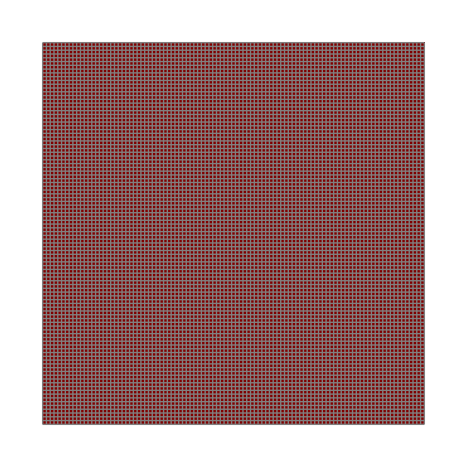

```mathematica
z=RandomReal[{0,255}];
octaves=6;
persistence=RandomReal[{0.5, 0.6}]
xcoef=RandomInteger[{0, 100}];ycoef=RandomInteger[{0,100}];
offset={0.37, 0.57};
(*noiseMap=Table[Mean[Flatten[Table[octavePerlin[a, b,z,octaves,persistence ], {a, x, x+10},{b, y, y+10}]]], {x, 1,100, 10},{y,1,100, 10}]*)
noiseMap=Table[octavePerlin[x+offset[[1]],y+0offset[[2]],z,octaves,persistence ],{x,xcoef,xcoef+5,0.05},{y,ycoef,ycoef+5,0.05}];
(*NEED TO FIGURE HOW TO MAKE THE NOISE THINGY ACC OKISH*)
classifyEntityTile[val_]:=Which[val<0.485,"park", val<0.52,"building", True, "background"];

tileColors=<|"road"->Black,"background"->White,"park" -> Green, "building"->Blue|>;
tileToNumber=AssociationThread[Keys[tileColors],Range[Length[tileColors]]];
tileMap=Map[classifyEntityTile,noiseMap,{2}];
MapGrid=Map[tileToNumber,tileMap,{2}];
(*numericGrid[[All,mid]]=1;*)

(*visualizeTileMap[tileMap_]:=Module[{tileColors=<|"road"->Gray,"building"->Darker[Red],"park"->LightGreen|>,tileNums,colorRules},tileNums=AssociationThread[Keys@tileColors,Range@Length@tileColors];
colorRules=Thread[Values@tileNums->Values@tileColors];
ArrayPlot[tileNums/@tileMap,ColorRules->colorRules,Frame->False,Mesh->True,MeshStyle->Gray]];*)

ArrayPlot[MapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False,Mesh->True,MeshStyle->Gray]
```

### Street/Road Structure generation(grid format)

```mathematica
MapGrid = Table[0, {x, worldWidth}, {y, worldHeight}];
roadsCoords = generateRoads[worldWidth,worldHeight,minBlock,maxJitter,roadWidth,noiseFreq,lowCutoff,highCutoff];
(*For[i=1, i<=Length[roadsCoords], i++,
Module[{x1=roadsCoords[[]][[1]], x2=roadsCoords[[3]],y1=roadsCoords[[2]],y2=roadsCoords[[4]], width=roadsCoords[[5]]},If[x1==x2,MapGrid=ReplacePart[MapGrid,{x1,j_}/;y1<j<y2->"R"],MapGrid=ReplacePart[MapGrid,{i_,y|1}/;x1<i<x2->"R"] ]]];*)
roadPutter[Coords_] := Module[{x1=Coords[[1]]//Floor, x2=Coords[[3]]//Floor,y1=Coords[[2]]//Floor,y2=Coords[[4]]//Floor, width=Coords[[5]]},If[x1==x2,MapGrid=ReplacePart[MapGrid,{x1,j_}/;y1<=j<=y2->1],MapGrid=ReplacePart[MapGrid,{i_,y1}/;x1<=i<=x2->1] ]];
roadPutter/@roadsCoords;
MapGrid//Grid;
```

### Visualize

```mathematica
ArrayPlot[MapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False(*,Mesh->True*)(*,MeshStyle->Gray*)]
```

-Graphics-

### perlin noise map

```mathematica
ClearAll[persistence,z,xcoef,zelev,ycoef,elevpers,elevnoiseMap,elevoctaves]
```

```mathematica
xcoef[]:=RandomInteger[{1,245}];
ycoef[]:=RandomInteger[{1,245}];
offset={0.37,0.57};
```

```mathematica
xcoef[]
```

63

```mathematica
|
```

```mathematica
elevoctaves=6;elevx=xcoef[];elevy=ycoef[];zelev=RandomReal[{0,255}];elevpers=RandomReal[{0.3,0.6}];
elevnoiseMap=ParallelTable[octavePerlin[x,y,zelev,elevoctaves,elevpers],{x,elevx,elevx+10,10/worldWidth},{y,elevy,elevy+10,10/worldHeight}];
```

```mathematica
poploctaves=6;poplx=xcoef[];poply=ycoef[];zpopl=RandomReal[{0,255}];poplpers=RandomReal[{0.3,0.6}];
poplnoiseMap=ParallelTable[octavePerlin[x,y,zpopl,poploctaves,poplpers],{x,poplx,poplx+10,10/worldWidth},{y,poply,poply+10,10/worldHeight}];

poproctaves=6;poprx=xcoef[];popry=ycoef[];zpopr=RandomReal[{0,255}];poprpers=RandomReal[{0.3,0.6}];
poprnoiseMap=ParallelTable[octavePerlin[x,y,zpopr,poproctaves,poprpers],{x,poprx,poprx+10,10/worldWidth},{y,popry,popry+10,10/worldHeight}];
```

```mathematica
Plot3D
```

```mathematica
ListPlot3D[elevnoiseMap]
```

-Graphics3D-

```mathematica
octavePerlin[1,1,z,elevoctaves,persistence[]]
```

0.513455

```mathematica
poplnoiseMap//Length
```

251

```mathematica
{y,ycoef[],ycoef[]+10,10/worldHeight}
```

{y,{1,0,1,0,1,0,1,0,0,0,1,1,0,1,1,0,1,0,1,1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,0,0,0,1,1,0,1,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,0,0,1,0,1,1,1,1,0,1,1,1,1,0,0,0,1,1,1,1,1,1,0,1,1,1,0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,1,0,1,1,1,0,0,0,0,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0,1,0,0,0,0,1,0,0,0,1,1,1,0,0,1,0,0,1,1,1,0,1,0,0,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,0,1,1,1,1,1,0,1,0,0,1,0,0,0,1,1,0,0,1,1,1,1,0,1,1,0,0,1,0,1,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,1,0,1,1,1,0,1,1,0,1,1,0,1,0,0,1,0,0,0},{10,10,10,11,11,10,11,10,10,11,10,11,11,10,10,11,11,10,11,10,10,11,10,11,10,10,10,10,10,10,10,11,10,10,10,10,11,10,10,11,11,11,11,10,10,11,10,11,11,11,10,11,10,11,10,11,11,11,11,11,10,10,10,11,11,11,10,10,10,10,10,11,10,11,11,11,10,10,11,10,10,11,10,11,10,10,10,10,11,11,10,10,11,10,10,10,11,10,10,10,11,10,11,11,10,10,11,11,11,10,11,10,10,10,11,11,11,10,11,11,10,10,11,10,11,11,10,10,11,11,11,10,11,11,10,11,10,11,10,11,11,10,10,11,10,10,11,10,10,11,11,10,11,10,10,10,11,10,10,10,11,10,10,11,10,11,10,11,11,11,10,11,10,10,11,10,10,10,11,10,10,10,11,11,11,11,10,10,10,11,10,11,11,11,10,11,10,10,11,11,11,11,11,11,11,10,11,10,11,11,10,11,11,10,10,10,11,11,11,10,11,10,10,11,11,11,10,10,10,10,11,10,11,11,10,10,10,10,11,10,11,10,11,10,11},1/50}

### zero blocks finder

```mathematica
visited=MapGrid;
zeroBlocks={};
findDownRight[x_,y_,grid_]:=Module[{i=x,j=y},
If[visited[[x,y]]==0,
Until[i>worldWidth,If[grid[[i,j]]!=1,i++,Break[]]];i--;Until[j>worldHeight,If[grid[[i,j]]!=1,j++,Break[]]];j--;visited=ReplacePart[visited,{a_,b_} /; x<=a<=i&&y<=b<=j->1];
AppendTo[zeroBlocks,{x, y, i, j}]]];

Table[findDownRight[x, y, MapGrid],{x,worldWidth},{y,worldHeight}];
zeroBlocks
```

{{1,1,28,16},{1,18,28,31},{1,33,13,56},{1,58,33,119},{1,121,28,135},{1,137,28,156},{1,158,13,186},{1,188,29,205},{1,207,29,220},{1,222,17,250},{15,33,28,56},{15,158,33,186},{19,222,29,250},{30,1,48,27},{30,29,67,56},{30,121,61,134},{30,136,48,156},{31,188,50,198},{31,200,50,217},{31,219,49,250},{35,58,47,88},{35,90,47,119},{35,158,61,169},{35,171,61,186},{49,58,67,68},{49,70,67,78},{49,80,67,88},{49,90,67,119},{50,1,67,27},{50,136,61,156},{51,219,63,250},{52,188,63,217},{63,121,89,139},{63,141,89,154},{63,156,90,167},{63,169,90,186},{65,188,123,250},{69,1,97,10},{69,12,85,31},{69,33,92,43},{69,45,92,63},{69,65,85,86},{69,88,95,102},{69,104,95,119},{87,12,97,31},{87,65,95,86},{91,121,123,138},{91,140,123,154},{92,156,106,186},{94,33,110,63},{97,65,112,93},{97,95,115,106},{97,108,115,119},{99,1,127,13},{99,15,127,31},{108,156,123,186},{112,33,127,63},{114,65,127,93},{117,95,127,119},{125,121,158,150},{125,152,144,180},{125,182,153,199},{125,201,136,219},{125,221,143,250},{129,1,156,17},{129,19,156,31},{129,33,140,57},{129,59,140,90},{129,92,140,119},{138,201,153,219},{142,33,156,57},{142,59,162,73},{142,75,162,90},{142,92,162,100},{142,102,162,119},{145,221,157,250},{146,152,156,180},{155,182,163,201},{155,203,182,219},{158,1,191,24},{158,26,173,57},{158,152,185,161},{158,163,185,180},{159,221,182,235},{159,237,182,250},{160,121,185,135},{160,137,185,150},{164,59,191,74},{164,76,191,87},{164,89,191,100},{164,102,191,119},{165,182,182,201},{175,26,191,57},{184,182,219,211},{184,213,250,250},{187,121,203,152},{187,154,198,180},{193,1,211,24},{193,26,218,58},{193,60,207,87},{193,89,220,107},{193,109,220,119},{200,154,221,170},{200,172,221,180},{205,121,221,152},{209,60,224,87},{213,1,222,24},{220,26,250,42},{220,44,250,58},{221,182,250,196},{221,198,250,211},{222,89,250,100},{222,102,250,119},{223,121,250,137},{223,139,250,148},{223,150,233,169},{223,171,250,180},{224,1,232,24},{226,60,250,75},{226,77,250,87},{234,1,250,24},{235,150,250,169}}

### zeroblocks assigner

```mathematica
(*land[n_]:=Which[n<.45,"park",n<.60,"lowrise",True,"highrise"];*)
highnoise=0.525;lownoise=0.45;
land[n_,pr_,pl_]:=Which[pr>=highnoise&&n<=highnoise&&pl<=lownoise,"park",pr<=highnoise&&n<=highnoise,"industrial",pr>=highnoise&&pl>=highnoise&&n<=highnoise,"commercial",n>=highnoise&&pl>=highnoise,"business",True,"residential"];
tileColors=<|"road"->Black,"background"->White,"park" -> Green, "residential"->Red,"industrial"->Darker[Green], "commercial"->Darker[Blue],"business"->Darker[Cyan]|>;
tileToNumber=AssociationThread[Keys[tileColors],{1,0,3,4,5,6,7}];
(*offset={0.37,0.57};
xcoef=0.05;ycoef=0.05;z[]:=RandomReal[{0,255}];*)
blockOctaves=6;blockPersistence=0.55;
```

```mathematica
ClearAll[getBlockMid,classifyBlock,applyBlockType]
```

```mathematica
getBlockMid[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},{Floor[Mean[{x1, x2}]], Floor[Mean[{y1, y2}]]}];(*classifyBlock[coords_]:=Module[{x=getBlockMid[coords][[1]],y=getBlockMid[coords][[2]]},land[octavePerlin[x*xcoef,y*ycoef,z[],blockOctaves,blockPersistence]]];*)
classifyBlock[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]], elevnoise,poprnoise,poplnoise},elevnoise=Mean[Flatten[elevnoiseMap[[x1;;x2,y1;;y2]]]];poprnoise=Mean[Flatten[poprnoiseMap[[x1;;x2,y1;;y2]]]];poplnoise=Mean[Flatten[poplnoiseMap[[x1;;x2,y1;;y2]]]];
land[elevnoise,poprnoise,poplnoise]]
applyBlockType[coords_]:=Module[{l=classifyBlock[coords],x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},MapGrid=ReplacePart[MapGrid,{a_,b_} /; x1<=a<=x2&&y1<=b<=y2->tileToNumber[l]]]
```

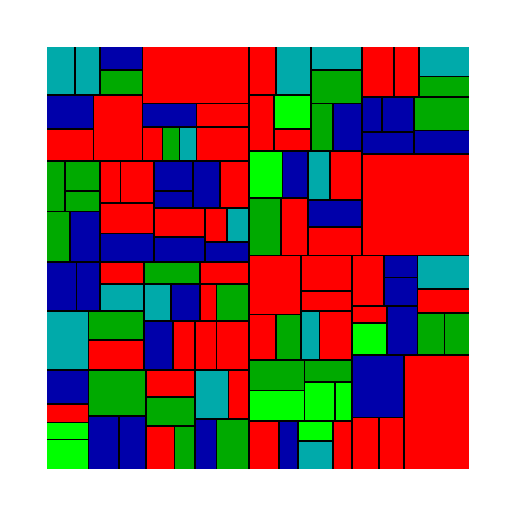

```mathematica
(*tileMap=Map[classifyEntityTile,noiseMap,{2}];
MapGrid=Map[tileToNumber,tileMap,{2}]*)
applyBlockType[#]&/@zeroBlocks;
ArrayPlot[MapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False(*,Mesh->True*)(*,MeshStyle->Gray*)]
```

### 3d visualization

#### give heights to each block

```mathematica
getElevationNoise[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},Mean[Flatten[elevnoiseMap[[x1;;x2,y1;;y2]]]]]
Table[AppendTo[zeroBlocks[[x]],Floor[Rescale[getElevationNoise[zeroBlocks[[x]]],{0.39,0.69},{1,10}]]],{x,zeroBlocks//Length}];
zeroBlocks;
```

{{1,1,28,16,5},{1,18,28,31,5},{1,33,13,56,2},{1,58,33,119,4},{1,121,28,135,6},{1,137,28,156,6},{1,158,13,186,6},{1,188,29,205,4},{1,207,29,220,5},{1,222,17,250,5},{15,33,28,56,2},{15,158,33,186,4},{19,222,29,250,2},{30,1,48,27,2},{30,29,67,56,5},{30,121,61,134,3},{30,136,48,156,3},{31,188,50,198,4},{31,200,50,217,4},{31,219,49,250,3},{35,58,47,88,3},{35,90,47,119,3},{35,158,61,169,4},{35,171,61,186,3},{49,58,67,68,3},{49,70,67,78,3},{49,80,67,88,5},{49,90,67,119,6},{50,1,67,27,4},{50,136,61,156,2},{51,219,63,250,4},{52,188,63,217,3},{63,121,89,139,3},{63,141,89,154,3},{63,156,90,167,5},{63,169,90,186,4},{65,188,123,250,4},{69,1,97,10,4},{69,12,85,31,3},{69,33,92,43,4},{69,45,92,63,2},{69,65,85,86,4},{69,88,95,102,4},{69,104,95,119,4},{87,12,97,31,3},{87,65,95,86,4},{91,121,123,138,3},{91,140,123,154,5},{92,156,106,186,3},{94,33,110,63,2},{97,65,112,93,3},{97,95,115,106,5},{97,108,115,119,7},{99,1,127,13,3},{99,15,127,31,4},{108,156,123,186,4},{112,33,127,63,3},{114,65,127,93,3},{117,95,127,119,4},{125,121,158,150,4},{125,152,144,180,2},{125,182,153,199,7},{125,201,136,219,2},{125,221,143,250,5},{129,1,156,17,4},{129,19,156,31,3},{129,33,140,57,5},{129,59,140,90,5},{129,92,140,119,5},{138,201,153,219,2},{142,33,156,57,5},{142,59,162,73,5},{142,75,162,90,3},{142,92,162,100,5},{142,102,162,119,3},{145,221,157,250,5},{146,152,156,180,2},{155,182,163,201,5},{155,203,182,219,3},{158,1,191,24,6},{158,26,173,57,3},{158,152,185,161,5},{158,163,185,180,3},{159,221,182,235,3},{159,237,182,250,2},{160,121,185,135,4},{160,137,185,150,3},{164,59,191,74,4},{164,76,191,87,5},{164,89,191,100,5},{164,102,191,119,4},{165,182,182,201,4},{175,26,191,57,4},{184,182,219,211,4},{184,213,250,250,4},{187,121,203,152,3},{187,154,198,180,3},{193,1,211,24,3},{193,26,218,58,4},{193,60,207,87,4},{193,89,220,107,5},{193,109,220,119,4},{200,154,221,170,1},{200,172,221,180,3},{205,121,221,152,2},{209,60,224,87,4},{213,1,222,24,1},{220,26,250,42,4},{220,44,250,58,4},{221,182,250,196,5},{221,198,250,211,5},{222,89,250,100,2},{222,102,250,119,4},{223,121,250,137,5},{223,139,250,148,4},{223,150,233,169,4},{223,171,250,180,5},{224,1,232,24,3},{226,60,250,75,7},{226,77,250,87,3},{234,1,250,24,3},{235,150,250,169,5}}

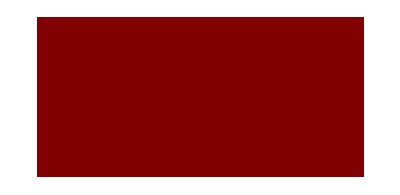

```mathematica
ArrayPlot[MapGrid2,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False(*,Mesh->True*)(*,MeshStyle->Gray*)]
```

blocks height(1-10)
- list of blocks
- give height to each block(add a num the end of the thingy)
roads need to be 1

### block height giver

```mathematica
ClearAll[blockHeightGiver]
blockHeightGiver[grid_,coords_,height_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]],h=coords[[5]]},If[height>h,ReplacePart[grid,{a_,b_} /; (x1<=a<=x2&&y1<=b<=y2)||grid[[a]][[b]]==1->tileToNumber["background"]],grid]]
```

```mathematica
(*COMMENT: TRY TO MAKE IT SO WE REMOVE IT BY 3D*)
```

```mathematica
MapGrid
```

```mathematica
ClearAll[MapGrid2];
MapGrid2=MapGrid;
MapGrid2=Table[blockHeightGiver[MapGrid2,zeroBlocks[[i]],7],{i,zeroBlocks//Length}];
```

```mathematica
MapGrid2
```

```mathematica
Table[MapGrid2=blockHeightGiver[MapGrid2,zeroBlocks[[i]],1],{i,zeroBlocks//Length}];
```

```mathematica
%180[[1]]
```

```mathematica
MapGrid2=MapGrid;
Table[MapGrid2=blockHeightGiver[MapGrid2,zeroBlocks[[i]],1],{i,zeroBlocks//Length}];
MapGrid3=MapGrid2;
Table[MapGrid3=blockHeightGiver[MapGrid3,zeroBlocks[[i]],2],{i,zeroBlocks//Length}];
MapGrid4=MapGrid3;
Table[MapGrid4=blockHeightGiver[MapGrid4,zeroBlocks[[i]],3],{i,zeroBlocks//Length}];
MapGrid5=MapGrid4;
Table[MapGrid5=blockHeightGiver[MapGrid5,zeroBlocks[[i]],4],{i,zeroBlocks//Length}];
MapGrid6=MapGrid5;
Table[MapGrid6=blockHeightGiver[MapGrid6,zeroBlocks[[i]],5],{i,zeroBlocks//Length}];
MapGrid7=MapGrid6;
Table[MapGrid7=blockHeightGiver[MapGrid7,zeroBlocks[[i]],6],{i,zeroBlocks//Length}];
MapGrid8=MapGrid7;
Table[MapGrid8=blockHeightGiver[MapGrid8,zeroBlocks[[i]],7],{i,zeroBlocks//Length}];
MapGrid9=MapGrid8;
Table[MapGrid9=blockHeightGiver[MapGrid9,zeroBlocks[[i]],8],{i,zeroBlocks//Length}];
MapGrid10=MapGrid9;
Table[MapGrid10=blockHeightGiver[MapGrid10,zeroBlocks[[i]],9],{i,zeroBlocks//Length}];
```

```mathematica
ArrayPlot3D[{MapGrid,MapGrid2,MapGrid3,MapGrid4,MapGrid5,MapGrid6,MapGrid7,MapGrid8,MapGrid9,MapGrid10},ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
{MapGrid,MapGrid2,MapGrid3,MapGrid4,MapGrid5,MapGrid6,MapGrid7,MapGrid8,MapGrid9,MapGrid10}
```

```mathematica
MapGrid//Length
```

250

```mathematica
mapGrid3D//Length
```

250

```mathematica
Counts[Flatten@MapGrid]
```

<|4→35181,1→5134,6→18448,7→3566,5→171|>

detail of blocks(adding buildings)
factor in:
- size of blocks
- noise population
-noise popularity
-elevation noise(3D)
- highrise vs lowrise(3D)
types of blocks:
- restaurants(cafe if low popularity)
- skyscrapers
- suburbs
-entertainments
-store

#### zeroblock testing

```mathematica
classifyBlock[{1, 1, 25, 44}]
land[0.55]
```

lowrise

lowrise

```mathematica
zeroBlocks={}
findDownRight[8, 2, MapGrid]
```

{}

9 2

10 2

11 2

{{8,2,10,3}}

```mathematica
|
```

```mathematica
MapGrid
```

{{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,0,1,1,0,0,1,0,0,0},{1,1,1,1,1,1,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,0,1,0,0,0}}

```mathematica
MapGrid//Grid
```

0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0

```mathematica
Position[MapGrid,0]
```

{{1,1},{1,2},{1,5},{1,6},{1,8},{1,9},{1,10},{2,1},{2,2},{2,5},{2,6},{2,8},{2,9},{2,10},{3,1},{3,2},{3,5},{3,6},{3,8},{3,9},{3,10},{4,1},{4,2},{4,5},{4,6},{4,8},{4,9},{4,10},{5,1},{5,2},{5,5},{5,6},{5,8},{5,9},{5,10},{6,1},{6,2},{6,5},{6,6},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,1},{8,2},{8,3},{8,5},{8,6},{8,8},{8,9},{8,10},{9,1},{9,2},{9,3},{9,5},{9,6},{9,8},{9,9},{9,10},{10,1},{10,2},{10,3},{10,5},{10,6},{10,8},{10,9},{10,10}}

```mathematica
If[TRue,fefef]
```

```mathematica
#==1
```

```mathematica
Apply
0001
0001
0001
1111
0000

1111
1111
1111
1111
0000
```

## cool image visualization(on hold)

```mathematica
z=RandomReal[{0,255}];
octaves=6;
persistence=RandomReal[{0.3, 0.6}]
(*noiseMap=Table[Mean[Flatten[Table[octavePerlin[a, b,z,octaves,persistence ], {a, x, x+10},{b, y, y+10}]]], {x, 1,100, 10},{y,1,100, 10}]*)
noiseMap=Table[octavePerlin[x,y,1,octaves,persistence ],{x,0.1,1,0.1},{y,0.1,1,0.1}]
(*NEED TO FIGURE HOW TO MAKE THE NOISE THINGY ACC OKISH*)
```